# Estudo do acoplamento em circuito duplo

## Antonio C. S. Lima setembro de 2020

## Determinação das matrizes de impedância

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Dropbox/UFRJ/cursos/CPE855/2020-1/arq_mma

```mathematica
aux=Table[If[i>j, z[i,j],0],{i,6},{j,6}];
aux1=Table[If[i==j, z[i,j],0],{i,6},{j,6}];
MatrixForm[Z=aux+Transpose[aux]+aux1]
```

(z[1,1] | z[2,1] | z[3,1] | z[4,1] | z[5,1] | z[6,1]
z[2,1] | z[2,2] | z[3,2] | z[4,2] | z[5,2] | z[6,2]
z[3,1] | z[3,2] | z[3,3] | z[4,3] | z[5,3] | z[6,3]
z[4,1] | z[4,2] | z[4,3] | z[4,4] | z[5,4] | z[6,4]
z[5,1] | z[5,2] | z[5,3] | z[5,4] | z[5,5] | z[6,5]
z[6,1] | z[6,2] | z[6,3] | z[6,4] | z[6,5] | z[6,6])

```mathematica
r={{0,1,0},{0,0,1},{1,0,0}};
transp=ArrayFlatten[{{r,0},{0,r}}];
MatrixForm[transp]
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0)

```mathematica
MatrixForm[zfinal=(Z+Inverse[transp].Z.transp+ Inverse[transp].( Inverse[transp].Z.transp).transp)/3]
```

(1/3 (z[1,1]+z[2,2]+z[3,3]) | 1/3 (z[2,1]+z[3,1]+z[3,2]) | 1/3 (z[2,1]+z[3,1]+z[3,2]) | 1/3 (z[4,1]+z[5,2]+z[6,3]) | 1/3 (z[4,3]+z[5,1]+z[6,2]) | 1/3 (z[4,2]+z[5,3]+z[6,1])
1/3 (z[2,1]+z[3,1]+z[3,2]) | 1/3 (z[1,1]+z[2,2]+z[3,3]) | 1/3 (z[2,1]+z[3,1]+z[3,2]) | 1/3 (z[4,2]+z[5,3]+z[6,1]) | 1/3 (z[4,1]+z[5,2]+z[6,3]) | 1/3 (z[4,3]+z[5,1]+z[6,2])
1/3 (z[2,1]+z[3,1]+z[3,2]) | 1/3 (z[2,1]+z[3,1]+z[3,2]) | 1/3 (z[1,1]+z[2,2]+z[3,3]) | 1/3 (z[4,3]+z[5,1]+z[6,2]) | 1/3 (z[4,2]+z[5,3]+z[6,1]) | 1/3 (z[4,1]+z[5,2]+z[6,3])
1/3 (z[4,1]+z[5,2]+z[6,3]) | 1/3 (z[4,2]+z[5,3]+z[6,1]) | 1/3 (z[4,3]+z[5,1]+z[6,2]) | 1/3 (z[4,4]+z[5,5]+z[6,6]) | 1/3 (z[5,4]+z[6,4]+z[6,5]) | 1/3 (z[5,4]+z[6,4]+z[6,5])
1/3 (z[4,3]+z[5,1]+z[6,2]) | 1/3 (z[4,1]+z[5,2]+z[6,3]) | 1/3 (z[4,2]+z[5,3]+z[6,1]) | 1/3 (z[5,4]+z[6,4]+z[6,5]) | 1/3 (z[4,4]+z[5,5]+z[6,6]) | 1/3 (z[5,4]+z[6,4]+z[6,5])
1/3 (z[4,2]+z[5,3]+z[6,1]) | 1/3 (z[4,3]+z[5,1]+z[6,2]) | 1/3 (z[4,1]+z[5,2]+z[6,3]) | 1/3 (z[5,4]+z[6,4]+z[6,5]) | 1/3 (z[5,4]+z[6,4]+z[6,5]) | 1/3 (z[4,4]+z[5,5]+z[6,6]))

```mathematica
a= Exp[I 120 Degree];
A={{1,1,1},{1,a^2,a},{1,a,a^2}};
Aplus=ArrayFlatten[{{A,0},{0,A}}];
MatrixForm[Aplus]
```

(1 | 1 | 1 | 0 | 0 | 0
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °) | 0 | 0 | 0
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °) | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
0 | 0 | 0 | 1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

```mathematica
z012=FullSimplify[Inverse[Aplus].zfinal.Aplus];
MatrixForm[z012]
```

(1/3 (z[1,1]+2 z[2,1]+z[2,2]+2 (z[3,1]+z[3,2])+z[3,3]) | 0 | 0 | 1/3 (z[4,1]+z[4,2]+z[4,3]+z[5,1]+z[5,2]+z[5,3]+z[6,1]+z[6,2]+z[6,3]) | 0 | 0
0 | 1/3 (z[1,1]-z[2,1]+z[2,2]-z[3,1]-z[3,2]+z[3,3]) | 0 | 0 | -((-1)^(1/6) (-z[4,2]+z[4,3]+z[5,1]-z[5,3]-z[6,1]+z[6,2]+(-1)^(1/3) (-z[4,1]+z[4,3]+z[5,1]-z[5,2]+z[6,2]-z[6,3])+2 (-1)^(2/3) (z[4,1]-z[4,2]+z[5,2]-z[5,3]-z[6,1]+z[6,3])))/(3 √3) | 0
0 | 0 | 1/3 (z[1,1]-z[2,1]+z[2,2]-z[3,1]-z[3,2]+z[3,3]) | 0 | 0 | -((-1)^(1/6) (z[4,2]-z[4,3]-z[5,1]+z[5,3]+z[6,1]-z[6,2]+(-1)^(1/3) (-z[4,1]+z[4,2]-z[5,2]+z[5,3]+z[6,1]-z[6,3])+2 (-1)^(2/3) (z[4,1]-z[4,3]-z[5,1]+z[5,2]-z[6,2]+z[6,3])))/(3 √3)
1/3 (z[4,1]+z[4,2]+z[4,3]+z[5,1]+z[5,2]+z[5,3]+z[6,1]+z[6,2]+z[6,3]) | 0 | 0 | 1/3 (z[4,4]+2 z[5,4]+z[5,5]+2 (z[6,4]+z[6,5])+z[6,6]) | 0 | 0
0 | -((-1)^(1/6) (z[4,2]-z[4,3]-z[5,1]+z[5,3]+z[6,1]-z[6,2]+(-1)^(1/3) (-z[4,1]+z[4,2]-z[5,2]+z[5,3]+z[6,1]-z[6,3])+2 (-1)^(2/3) (z[4,1]-z[4,3]-z[5,1]+z[5,2]-z[6,2]+z[6,3])))/(3 √3) | 0 | 0 | 1/3 (z[4,4]-z[5,4]+z[5,5]-z[6,4]-z[6,5]+z[6,6]) | 0
0 | 0 | -((-1)^(1/6) (-z[4,2]+z[4,3]+z[5,1]-z[5,3]-z[6,1]+z[6,2]+(-1)^(1/3) (-z[4,1]+z[4,3]+z[5,1]-z[5,2]+z[6,2]-z[6,3])+2 (-1)^(2/3) (z[4,1]-z[4,2]+z[5,2]-z[5,3]-z[6,1]+z[6,3])))/(3 √3) | 0 | 0 | 1/3 (z[4,4]-z[5,4]+z[5,5]-z[6,4]-z[6,5]+z[6,6]))

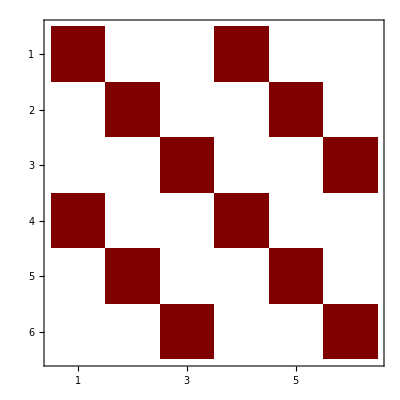

```mathematica
MatrixPlot[FullSimplify@z012]
```

```mathematica
θ= 360 Degree;
n= 6;
```

```mathematica
anovo= Exp[I θ/n];
```

```mathematica
(*
A6fasestr={
{1,1,1,1,1,1},
{1, a^(n-1), a^(n-2), a^(n-3), a^(n-4), a^(n-5)},
{1, a^(n-2), a^(n-4), a^(n-6), a^(n-8), a^2},
{1, a^(n-4), a^(n-8), a^(n-12), a^(n-16)

*)
```